```mathematica
NN = 3000
Λ = 10
2.0 Log[Λ/m0]
Λ^2
cc[k_]  :=  Exp[ (ⅈ 2 π k)/NN]
circ= Array[cc, NN, 0];
Needs["PlotLegends`"]
```

3000

10

2. Log[10/m0]

100

```mathematica
sys[u_, m_] := {    1/NN ∑_(k=0)^(NN-1) Log [ DD + (σ - m circ[[k+1]])(σ - Conjugate[m circ[[k+1]]])] ==Log [ Λ^2],
            1/NN ∑_(k=0)^(NN-1) (σ - m circ[[k+1]]) Log [ 1 + DD/((σ - m circ[[k+1]])(σ - Conjugate[m circ[[k+1]]]))] == u σ };
sol[u_, m_]:=FindRoot[sys[u,m],{ σ , Λ Exp [ (- u)/2.0]2.0}, {DD,Λ^2 ( 1 - Exp[-u])2.0}]
sig[u_,m_]:= σ /. sol[u, m]
dd[u_, m_] := DD /. sol[u,m]
```

```mathematica
sysappr[u_,m_] := { σ Log [ Λ^2/σ^2] - m^2/σ  == u σ }
solappr[u_,m_] := FindRoot[sysappr[u,m],{ σ , Λ Exp [ (- u)/2.0]2.0}];
asig[u_,m_] := σ /. solappr[u,m]
```

```mathematica
u= 2.0
m = 0.02
Λ Exp[-(u+1)/2]
```

2.

0.02

2.2313

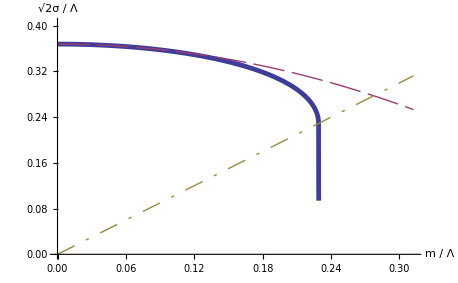

```mathematica
Plot[{sig[u, ml Λ] / Λ,( ⅇ^(-u/2)  - (ml Λ)^2/Λ^2 Sinh[u/2]), ml},{ml, 0.0 / Λ, 1.4 Exp[ -(u+1)/2]}, PlotRange->{0.0, 1.1 ⅇ^(-u/2)}, 
          PlotStyle->{Thickness[0.0075], {Thick, Dashing[{0.05,0.012}]}, {Thick, Dashing[{0.03,0.02,0.005, 0.02}]}},
	AxesLabel->{ Style["m / Λ",FontSize->15], Style["√2σ / Λ",FontSize->15]}]
```

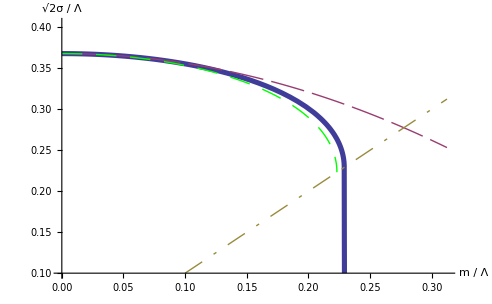

```mathematica
Show[   %, Plot[{asig[ u, ml Λ ] / Λ}, {ml, 0.0, ⅇ^(-(u+1)/2)}, PlotStyle->{{Thick,Dashing[{0.03,0.02}],Green}}]   ]
```

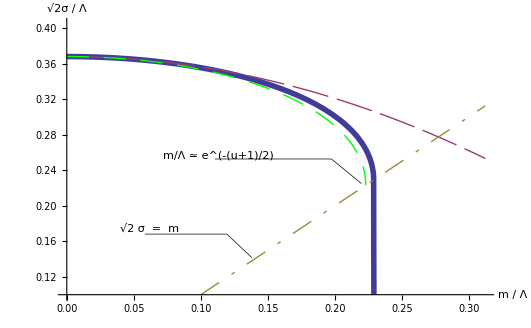

```mathematica
m=0.02
```

0.02

```mathematica
Subscript[m, min] = 0.0;
Subscript[m, max]= 1.4 Exp[ -(u+1)/2] Λ;
MM = 50;
dm = (Subscript[m, max] - Subscript[m, min])/MM;
mpos =Table[Null,{MM}];
ssig = Table[Null,{MM}];
ddd = Table[Null, {MM}];
addd = Table[Null, {MM}];
EEE = Table[Null,{MM}];
sigcorr = Table[Null, {MM}];
assig = Table[Null, {MM}];
abssq[k_,l_] := (Abs[ ssig[[l+1]] - mpos[[l+1]] circ[[k+1]]])^2
```

```mathematica
For [ l = 0, l < MM, l++, 
mpos[[l+1]] = Subscript[m, min] + dm l;
ssig[[l+1]] = sig[u, mpos[[l+1]] ];
ddd[[l+1]] = dd[u,mpos[[l+1]] ];
addd[[l+1]] = Λ^2 - (ssig[[l+1]])^2 - (mpos[[l+1]])^2;
EEE[[l+1]] = 1/NN∑_(k=0)^(NN-1) (abssq[k,l] Log[ abssq[k,l]/Λ^2] -( ddd[[l+1]] + abssq[k,l]) Log [ (ddd[[l+1]] +abssq[k,l])/Λ^2] ) + ddd[[l+1]] + u (Abs[ssig[[l+1]]])^2;
EEE[[l+1]] = 1/Λ^2 EEE[[l+1]];
sigcorr[[l+1]] = Λ( ⅇ^(-u/2)  - (mpos[[l+1]])^2/Λ^2 Sinh[u/2]);
assig[[l+1]] = asig[u,mpos[[l+1]]];
];
Evsm = Partition[Riffle[mpos / Λ,EEE ],2];
mvsm = Partition[Riffle[mpos / Λ,mpos / Λ],2];
sigvsm = Partition[Riffle[mpos,ssig],2];
sigcorrvsm = Partition[Riffle[mpos,sigcorr],2];
dvsm = Partition[Riffle[mpos,ddd],2];
assigvsm = Partition[Riffle[mpos,assig],2];
adddvsm = Partition[Riffle[mpos, addd], 2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

```mathematica
Ecoulomb = Table[Null,{MM}];
Ecoloumb = (mpos/Λ)^2(Log[ (mpos/Λ)^2] - 1) + 1;
```

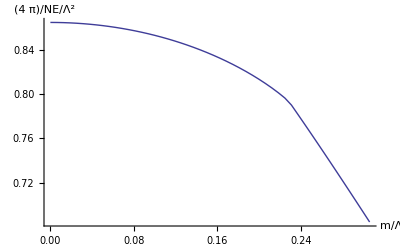

```mathematica
ListPlot[Evsm, Joined->True, PlotStyle->Thick,AxesLabel->{Style["m/Λ",FontSize->15],Style["(4  π)/NE/Λ^2",FontSize->15]}]
```

```mathematica
Show[%,Plot[μ^2 (  - 1. + Log[ μ^2 ] ) + 1, { μ,0., 1.4 ⅇ^(- (u+1)/2)}, PlotStyle->{{Thick,Green, Dashing[{0.01}]}}, PlotRange->{Automatic,{Automatic,1 - ⅇ^-u}}]]
```

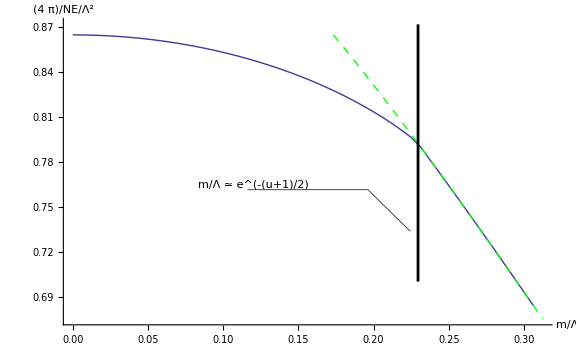

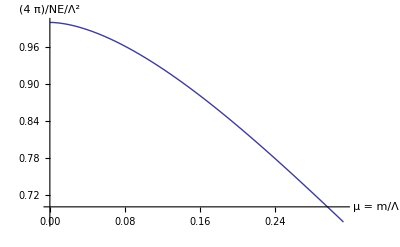

```mathematica
Plot[ μ^2 (  - 1. + Log[ μ^2 ] ) + 1, {μ, 0., 1.4 ⅇ^(- (u+1)/2)}, PlotStyle->Thick , PlotLegend-> {Style["μ^2 ( ln(μ^2) - 1 ) + 1", FontSize->15]},
            AxesLabel->{Style["μ = m/Λ",FontSize->15],Style["(4  π)/NE/Λ^2",FontSize->15]}]
```

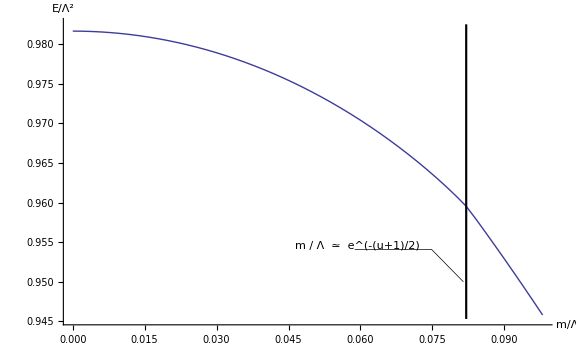

-Graphics-

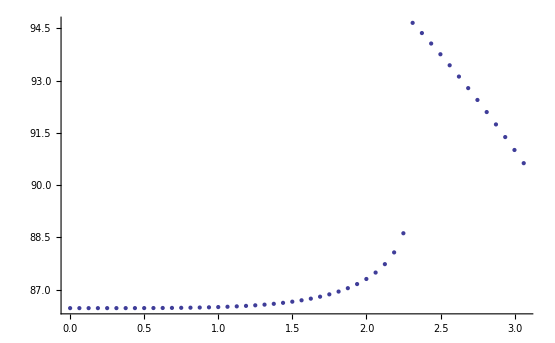

```mathematica
ListPlot[dvsm]
```

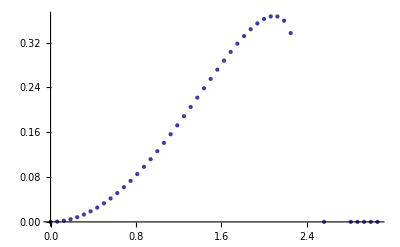

```mathematica
ListPlot[ Table[ {mpos[[n]], ddd[[n]] -addd[[n]]}, {n,1,50} ] ]
```

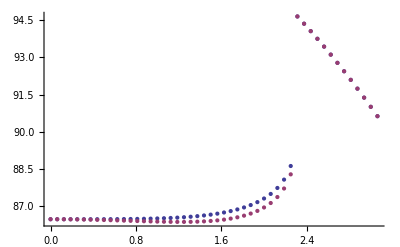

```mathematica
ListPlot[{dvsm,adddvsm}]
```

```mathematica
Λ ⅇ^(-u/2)
```

3.67879